```mathematica
s1=RandomVariate[MultinormalDistribution[{1,1,2},{{1,0,0},{0,1,0},{0,0,1}}],100];
s2=RandomVariate[MultinormalDistribution[{-1,-1,-1},{{1,0,0},{0,1,0},{0,0,1}}],100];
```

```mathematica
ss=Join[s1,s2];
Dimensions[ssᵀ]
```

{3,200}

```mathematica
x=ss;
xc=Table[x[[i,All]]-Mean[x[[i]]],{i,Length[x]}];
```

```mathematica
t1=AbsoluteTime[];
cov=xc.xcᵀ/(Length[x[[1]]]-1)//Timing
t2=AbsoluteTime[]-t1
```

{1.26288×10^-15,{{1.58247,-0.394496,1.01418,«195»,0.402074,0.53658},«198»,{«1»}}}

0.328125

```mathematica
i=1;
While[i<10,Covariance[xcᵀ];i++]//Timing
i=1;While[i<10,cov=xc.xcᵀ/(Length[x[[1]]]-1);i++]//Timing
```

{1.38778×10^-17,Null}

{0.015,Null}

```mathematica
∑x[[i]]
```

Sum::argmu: Sum called with 1 argument; 2 or more arguments are expected.

Sum[x⟦i⟧]

```mathematica
op={dds->None};
(dds/.op)==None
```

True

```mathematica
(*ROC opt test*)
```

```mathematica
seed=3;
SeedRandom[seed];
μp=RandomReal[{-1,1},{2}];μn=RandomReal[{-1,1},{2}];
σp=RandomReal[{0.25,1}];σn=RandomReal[{0.25,1}];
xp=Map[Function[x,x+μp],RandomReal[NormalDistribution[0,σp],{1000,2}]];
xn=Map[Function[x,x+μn],RandomReal[NormalDistribution[0,σn],{1000,2}]];
truth=Join[ConstantArray[1,{1000}],ConstantArray[-1,{1000}]];

classifier=PseudoInverse[Map[Function[x,Append[x,1.]],Join[xp,xn]]].truth;

prediction=Map[Function[x,Append[x,1.]],Join[xp,xn]].classifier;
```

```mathematica
truth;
```

```mathematica
prediction;
```

```mathematica
x=Sort[RandomReal[1,50,WorkingPrecision->1]];
y=Sort[RandomReal[1,50,WorkingPrecision->1]];
Length[x]
Length[y]
```

50

50

```mathematica
Length[Union[x]]
Union[x]
```

15

{0,0.06,0.1,0.2,0.3,0.3,0.4,0.4,0.5,0.6,0.7,0.8,0.8,0.9,0.9}

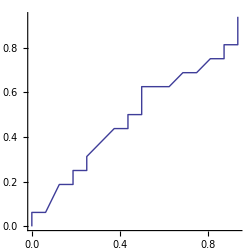

-Graphics-

```mathematica
ss={x,y}ᵀ;
ListPlot[ss,Joined->True,AspectRatio->1]
ListPlot[Union[ss],Joined->True,AspectRatio->1]
```